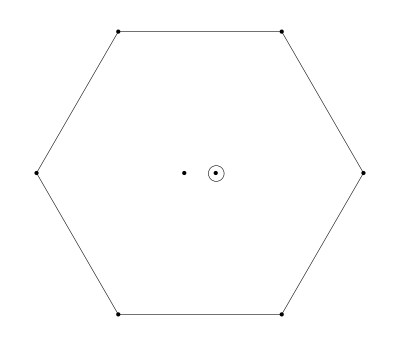

Y=0,  I_3=0

(ud-du)(d̄ū-ūd̄)+2(ds-sd)(d̄s̄-s̄d̄)+(us-su)(s̄ū-ūs̄)

```mathematica
(*-------------------------------*)
```

The current J:

2 (d_a^T C γ^μ s_b-s_a^T C γ^μ d_b) ((d̄)_a γ^μ C((s̄)_b)^T)+2 (d_a^T C γ^μ s_b-s_a^T C γ^μ d_b) ((d̄)_b γ^μ C((s̄)_a)^T)+2 (s_a^T C γ^μ d_b-d_a^T C γ^μ s_b) ((s̄)_a γ^μ C((d̄)_b)^T)+2 (s_a^T C γ^μ d_b-d_a^T C γ^μ s_b) ((s̄)_b γ^μ C((d̄)_a)^T)+(u_a^T C γ^μ d_b) ((d̄)_a γ^μ C((ū)_b)^T-(ū)_a γ^μ C((d̄)_b)^T)+(d_a^T C γ^μ u_b) ((ū)_a γ^μ C((d̄)_b)^T-(d̄)_a γ^μ C((ū)_b)^T)+(u_a^T C γ^μ d_b) ((d̄)_b γ^μ C((ū)_a)^T-(ū)_b γ^μ C((d̄)_a)^T)+(d_a^T C γ^μ u_b) ((ū)_b γ^μ C((d̄)_a)^T-(d̄)_b γ^μ C((ū)_a)^T)+(u_a^T C γ^μ s_b) ((s̄)_a γ^μ C((ū)_b)^T-(ū)_a γ^μ C((s̄)_b)^T)+(s_a^T C γ^μ u_b) ((ū)_a γ^μ C((s̄)_b)^T-(s̄)_a γ^μ C((ū)_b)^T)+(u_a^T C γ^μ s_b) ((s̄)_b γ^μ C((ū)_a)^T-(ū)_b γ^μ C((s̄)_a)^T)+(s_a^T C γ^μ u_b) ((ū)_b γ^μ C((s̄)_a)^T-(s̄)_b γ^μ C((ū)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-4 (d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s)+4 (d̄(γ^μ).(γ̄)^5 s s̄(γ^μ).(γ̄)^5 d)+4 (d̄ γ^μ d s̄ γ^μ s)-4 (d̄ γ^μ s s̄ γ^μ d)+8 (d̄(γ̄)^5 s s̄(γ̄)^5 d)+4 (d̄(γ̄)^5 d) (ū(γ̄)^5 u-2 (s̄(γ̄)^5 s))+4 (d̄ 1d) (2 (s̄ 1s)-ū 1u)-8 (d̄ 1s s̄ 1d)+2 (d̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)-2 (d̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)-2 (d̄ γ^μ d ū γ^μ u)+2 (d̄ γ^μ u ū γ^μ d)-4 (d̄(γ̄)^5 u ū(γ̄)^5 d)+4 (d̄ 1u ū 1d)+2 (s̄(γ^μ).(γ̄)^5 s ū(γ^μ).(γ̄)^5 u)-2 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 s)-2 (s̄ γ^μ s ū γ^μ u)+2 (s̄ γ^μ u ū γ^μ s)+4 (s̄(γ̄)^5 s ū(γ̄)^5 u)-4 (s̄(γ̄)^5 u ū(γ̄)^5 s)-4 (s̄ 1s ū 1u)+4 (s̄ 1u ū 1s)
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(80 π^6)-(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(8 π^5)+(2 ⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-2 m_u) q^4)/(3 π^4)-(2 ⟨ d̄ d⟩ log(-q^2/μ^2) (5 m_d-4 m_s-m_u) q^4)/(3 π^4)+(2 ⟨ s̄ s⟩ log(-q^2/μ^2) (4 m_d-5 m_s+m_u) q^4)/(3 π^4)-(160 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(160 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(64 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(113 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(144 π^6)-(128 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(112 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(112 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(8 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(2 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(3 π^2)-(8 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)-(2 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(3 π^2)-(2 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(2 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(3 π^2)-(160 ⟨ GG ⟩ ⟨ d̄ d⟩^2)/(9 π q^2)-(160 ⟨ GG ⟩ ⟨ s̄ s⟩^2)/(9 π q^2)-(64 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(80 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(9 π q^2)+(124 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(9 π q^2)+(124 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(9 π q^2)+(5 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(12 π^2 q^2)+(5 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(48 π^2 q^2)+(5 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(48 π^2 q^2)-(256 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 (8 m_d+m_s))/(9 q^2)-(256 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ (m_d+8 m_s))/(9 q^2)+(512 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (2 m_d+2 m_s-m_u))/(3 q^2)-(64 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (8 m_d+m_u))/(9 q^2)-(64 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (8 m_s+m_u))/(9 q^2)-(64 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+8 m_u))/(9 q^2)-(64 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (m_s+8 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=ρ_8=ρ_10=1

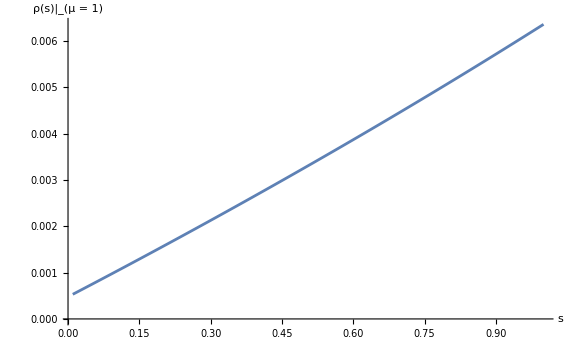
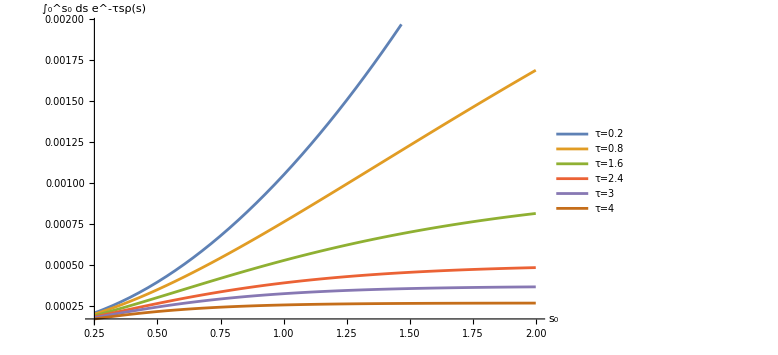

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=ρ_8=ρ_10=1

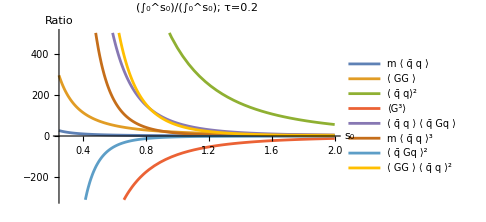
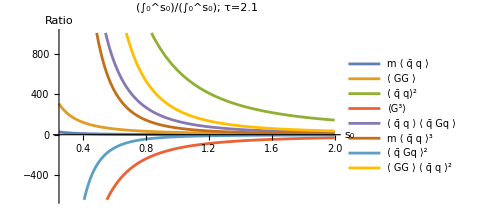
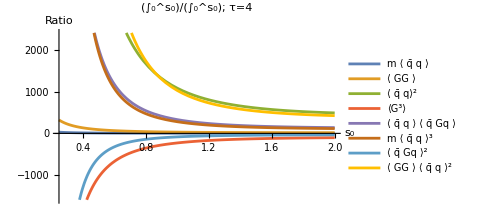

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=ρ_8=ρ_10=1

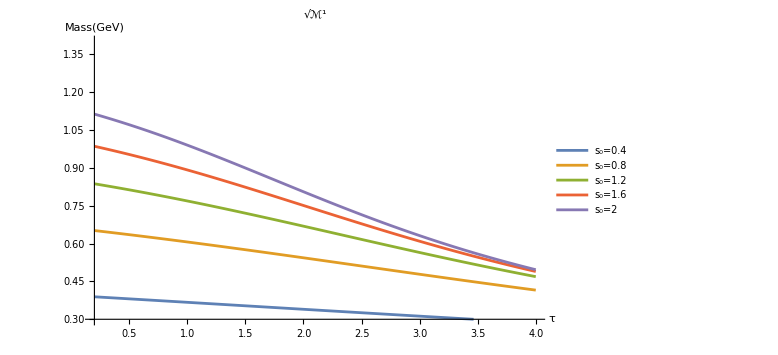
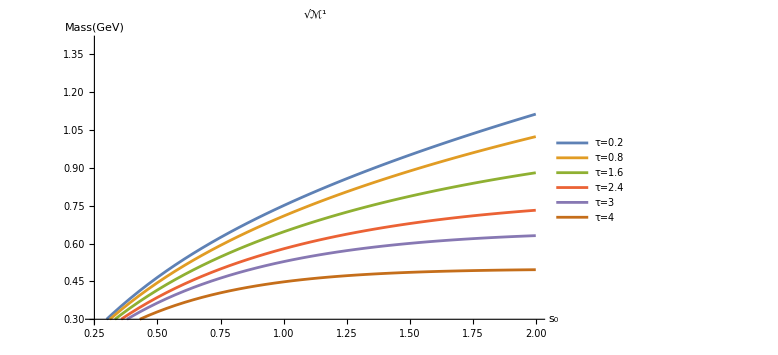

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=ρ_8=ρ_10=1

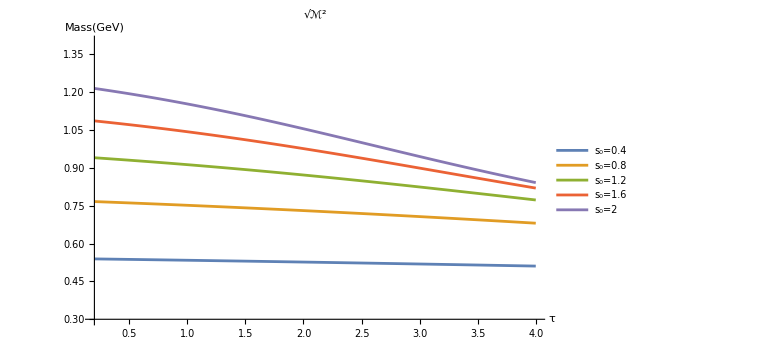
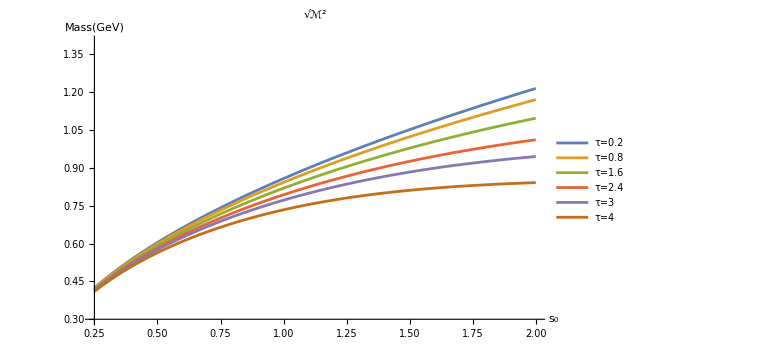

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for ρ_6=3, ρ_8=5, ρ_10=5

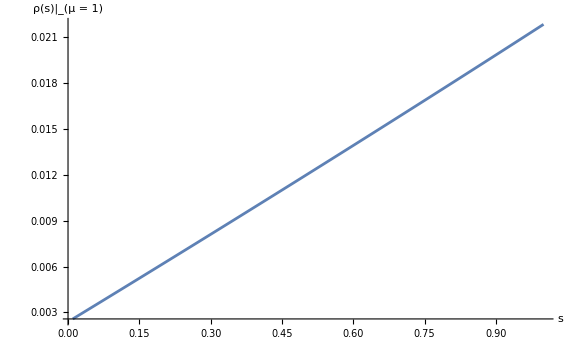
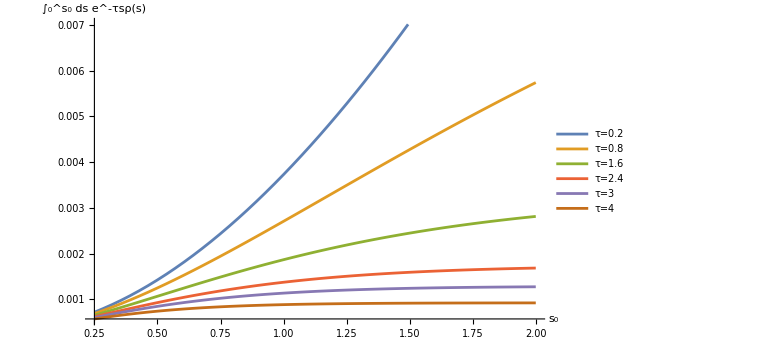

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for ρ_6=3, ρ_8=5, ρ_10=5

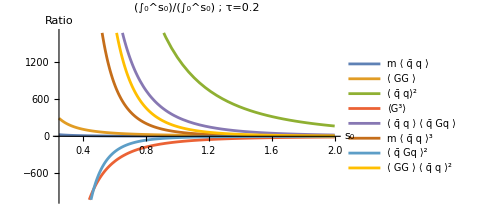
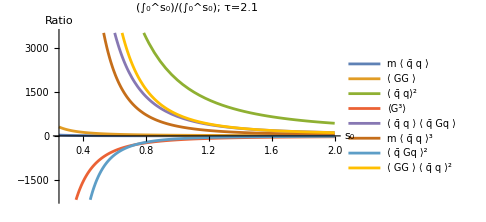
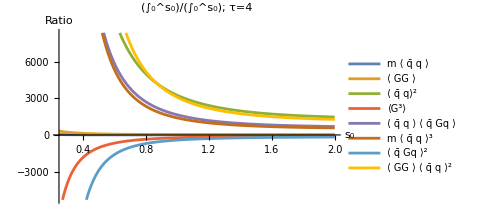

```mathematica
(*-------------------------------*)
```

ℛ^0 for ρ_6=3, ρ_8=5, ρ_10=5

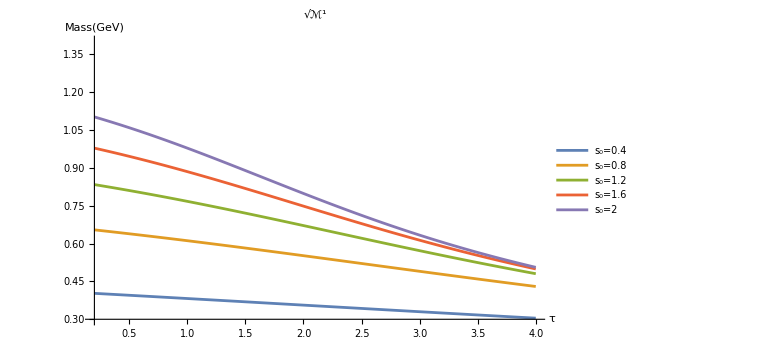
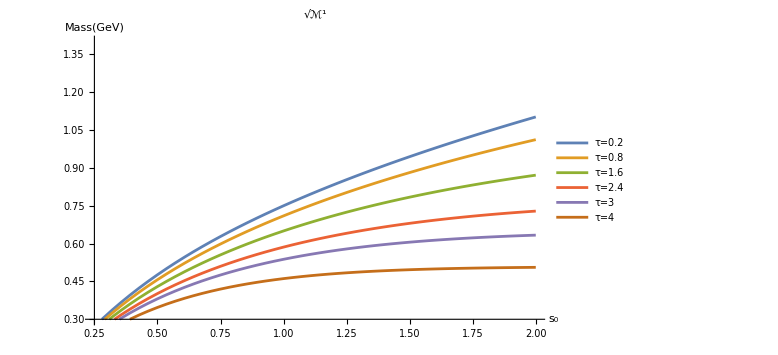

```mathematica
(*-------------------------------*)
```

ℛ^1 for ρ_6=3, ρ_8=5, ρ_10=5